```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
md={{0.038919565918040445,0.06743682653727344},{0.12582094383686163,0.10923208048614581},{0.1892583277055926,0.12852782269560006},{0.30988003094936495,0.18358091276753688},{0.48025965960625705,0.1479696311077649},{0.49657169002278573,0.1791783591997105},{0.6465066249674667,0.1798587912586749}};
σmd={0.2088095376752115,0.21706712111822724,0.22532470456124298,0.23564668386501264,0.2459686631687824,0.2500974548902902,0.26496110508771864};
σmderr={0.01621039222655274,0.015928132568206136,0.015645872909859533,0.015293048336926279,0.014940223763993024,0.014799093934819724,0.014291026549795836};
βvals={6.8,6.9,7,7.125,7.25,7.3,7.48};
Tvals={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
αcont={0.5138562580709736,0.0027118637679895965};
σcont={0.16949622818854412,0.0009172672238755708};
ccont={-0.15942304870711493,0.0023023051670536016};
```

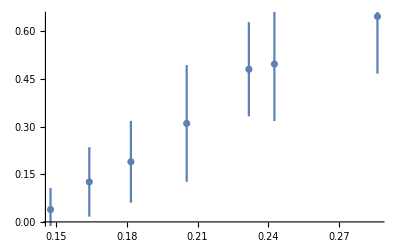

```mathematica
ErrorListPlot[Transpose[{Tvals,md[[All,1]],md[[All,2]]}]]
```

```mathematica
as[Nc_,Nf_,T_,μ_]:=(12π)/((11 Nc-2 Nf )Log[(2π √(T^2+μ^2/π^2))/0.176]);
```

```mathematica
ngam[x_]:=PolyGamma[1/2-ⅈ x]+PolyGamma[1/2+ⅈ x];
```

```mathematica
mDlo[Nc_,Nf_,T_,μ_]:=Sqrt[4 π as[Nc,Nf,T,μ](Nf(T^2/6+μ^2/(2π))+(Nc T^2)/3)];
```

```mathematica
mDnlo[Nc_,Nf_,T_,μ_,c_,d_]:=Re[(4π)/3 as[Nc,Nf,T,μ] T^2(Nc+(Nc^2 as[Nc,Nf,T,μ])/(12π)(5+22 EulerGamma+22Log[(2π √(T^2+μ^2/π^2))/(4π T)])+Nf/2(1+12 μ^2/(2π T)^2)+(Nc Nf as[Nc,Nf,T,μ])/(24π)((9+132 μ^2/(2π T)^2)+22EulerGamma(1+12 μ^2/(2π T)^2)+2(7+132 μ^2/(2π T)^2)Log[(2π √(T^2+μ^2/π^2))/(4π T)]+4ngam[μ/(2π T)])+(Nf^2 as[Nc,Nf,T,μ])/(12π)(1+12 μ^2/(2π T)^2)(1-2Log[(2π √(T^2+μ^2/π^2))/(4π T)]+ngam[μ/(2π T)])-3/(8π)(Nf(Nc^2-1)as[Nc,Nf,T,μ])/Nc(1+12 μ^2/(2π T)^2)+c as[Nc,Nf,T,μ]^2+d as[Nc,Nf,T,μ]^4)];
```

```mathematica
mDcal[T_,μ_,c_,d_,Nc_,Nf_]:=(Re[Sqrt[Nc/3+Nf/6+Nf/(2 π^2)(μ/3)^2/T^2] √(4π as[Nc,Nf,T,μ])T+Nc as[Nc,Nf,T,μ] T Log[Sqrt[Nc/3+Nf/6]/as[3,3,T,0]]+c 4π as[Nc,Nf,T,μ] T+d (4π as[Nc,Nf,T,μ])^(3/2)T ])^1;
```

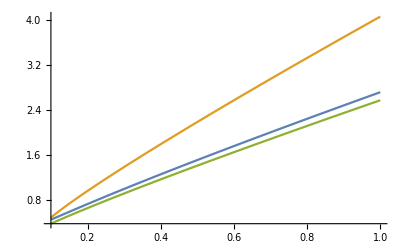

```mathematica
Plot[{mDlo[3,3,x,0.],mDcal[x,0.,0,0,3,3],mDnlo[3,3,x,0.,0,0]},{x,0.1,1.}]
```

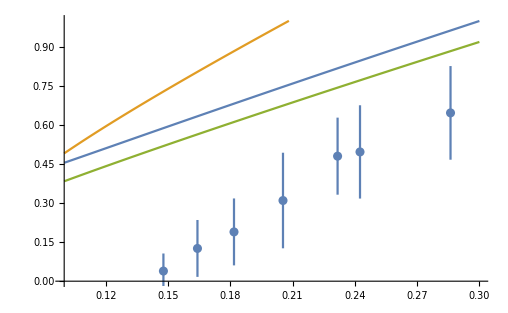

```mathematica
Show[{Plot[{mDlo[3,3,x,0.],mDcal[x,0.,0,0,3,3],mDnlo[3,3,x,0.,0,0]},{x,0.1,0.3},PlotRange->{0.,1.}],ErrorListPlot[Transpose[{Tvals,md[[All,1]],md[[All,2]]}]]}]
```

```mathematica
mDfit=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),(md[[n,1]] √(σcont[[1]]/σmd[[n]]))^2},{n,1,Length[Tvals]}],mDnlo[3,3,x,0.,d,e],{d,e},x];
{k1,k2}={d,e}/.mDfit["BestFitParameters"];
mDfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | -6.63885 | 0.387822 | -17.1183 | 0.0000124524
e | 2.72388 | 0.681049 | 3.99953 | 0.0103282

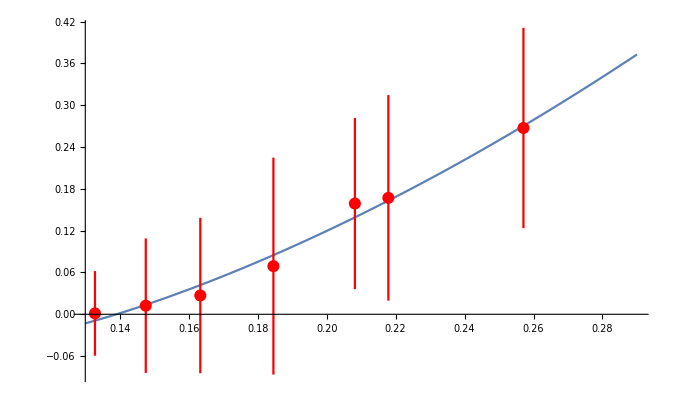

```mathematica
Show[{Plot[mDnlo[3,3,x,0.,k1,k2],{x,0.13,0.29},PlotRange->All],ErrorListPlot[Table[{Tvals[[n]](155/172.5),(md[[n,1]] √(σcont[[1]]/σmd[[n]]))^2,md[[n,2]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],PlotRange->All,PlotStyle->{Red}]}]
```

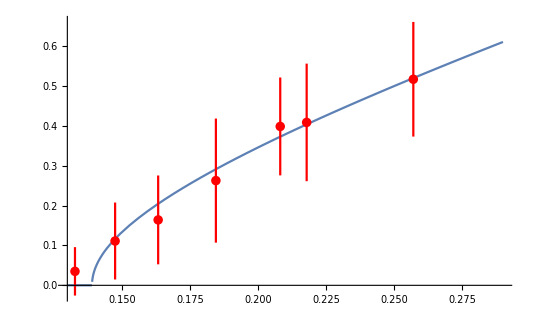

```mathematica
Show[{Plot[Re[Sqrt[mDnlo[3,3,x,0.,k1,k2]]],{x,0.13,0.29},PlotRange->All],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]] √(σcont[[1]]/σmd[[n]]),md[[n,2]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],PlotRange->All,PlotStyle->{Red}]}]
```

```mathematica
Re[Sqrt[mDnlo[3,3,0.155,0.,k1,k2]]]
```

0.162734

```mathematica
Re[Sqrt[mDnlo[3,3,0.155,0.3,k1,k2]]]
```

0.557733